# Different Distribution Types

## Types of Distributions

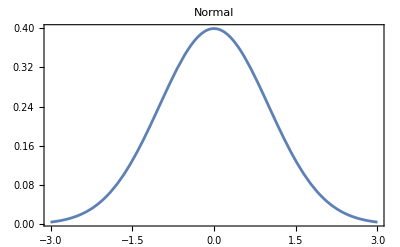
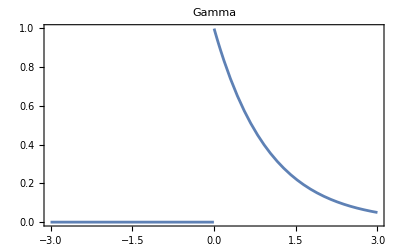
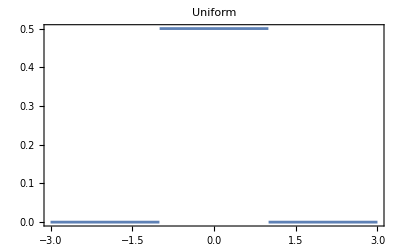
Distribution | Formula | Graph | Description
Normal |  | -Graphics- | The normal distribution is the classic probability distribution. It's continuous, centered around its mean, μ, with a standard deviation, σ.
Gamma |  | -Graphics- | The gamma distribution is another continuous probability distribution with two parameters. Instead of μ and σ, the Gamma distribution works with α, the shape parameter, and β, the rate parameter. Note that both of these parameters must be
Uniform |  | -Graphics- | The uniform distribution is yet another continuous distribution, however it differs from both the Normal and Gamma distributions in that all outcomes are equally likely within the range of the function.

```mathematica
initializations={{"Normal","",NormalDistribution[],"The normal distribution is the classic probability distribution. It's continuous, centered around its mean, μ, with a standard deviation, σ."},{"Gamma","",GammaDistribution[1,1],"The gamma distribution is another continuous probability distribution with two parameters. Instead of μ and σ, the Gamma distribution works with α, the shape parameter, and β, the rate parameter. Note that both of these parameters must be"},{"Uniform","",UniformDistribution[{-1,1}],"The uniform distribution is yet another continuous distribution, however it differs from both the Normal and Gamma distributions in that all outcomes are equally likely within the range of the function."}};
distributionPlots=Function[{init},{init[[1]],init[[2]],Plot[PDF[init[[3]],x],{x,-3,3},PlotLabel->init[[1]],PlotRange->All,Frame->True,FrameTicks->None],init[[4]]}]/@initializations;
initializationGrid=Grid[Prepend[distributionPlots,{"Distribution","Formula","Graph","Description"}],Frame->All,Alignment->{Center,Center}];
initializationGrid
```

## Explanation

These are the different types of initial distributions this project will be testing. The point is to examine the effects of initializing weights from each distribution type on the distribution of outputs, and the different characteristics of each distribution is where the explanations will be derived from. For starters, the Gamma distribution doesn’t work with negative values, so initializing weights from this distribution will result in only positive weights. The uniform distribution will increase the likelihood of extreme weights, and it will be useful to see if this increases the frequency/”messiness” of the output graphs.

## Normal Distribution

### Defining Normal Distribution Function

```mathematica
normalNetworkPlot[activations_,depths_,sigma_]:=Module[{netPlots,netInit,f,plots,act,depth},netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[4];
SeedRandom[1234];
plots=Append[Prepend[netPlots,""]]@Table[Prepend[Text[act/. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->NormalDistribution[0,sigma],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths}],{act,activations}];
Grid[plots]
]
```

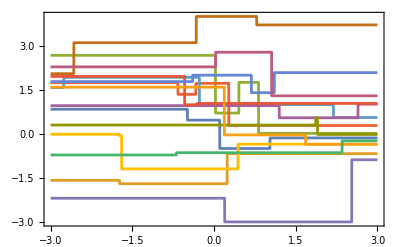
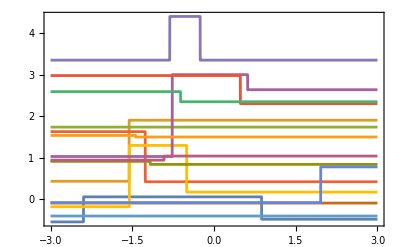
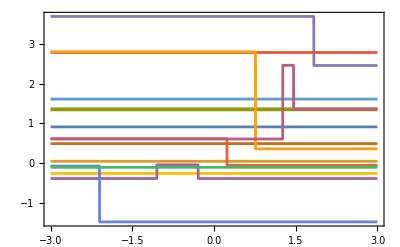
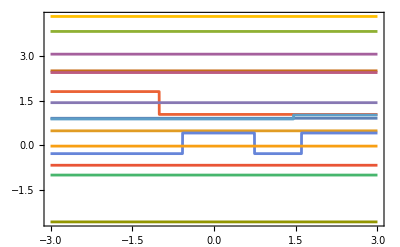
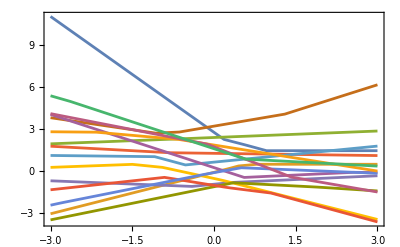
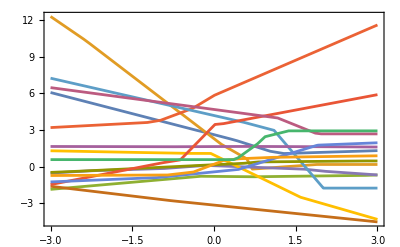
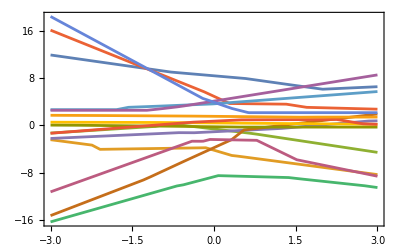
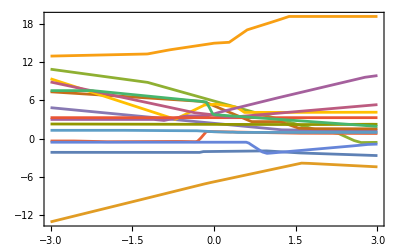
Threshold | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Ramp | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Tanh | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Sin | -Graphics- | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
normalNetworkPlot[{Function[x,If[x>0,1,0]],Ramp,Tanh,Sin,LogisticSigmoid},{1,2,3,4},1]
```

### Finding Optimal Standard Deviation for different Network Depths and Activation Functions

```mathematica
normalInitializeNet[stdDev_,activation_,depth_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->NormalDistribution[0,stdDev],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
```

```mathematica
normalEvaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
```

```mathematica
stdDevs=Range[0.5,10,0.5];
normalMeasureVariance[activation_,depth_]:=Table[With[{netInit=normalInitializeNet[stdDev,activation,depth]},{stdDev,Mean[Table[Module[{outputs=normalEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]}],{stdDev,stdDevs}];
normalMeasureVarianceplotted[activation_,depth_]:=Table[With[{netInit=normalInitializeNet[stdDev,activation,depth]},Mean[Table[Module[{outputs=normalEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]],{stdDev,stdDevs}];
```

```mathematica
normalOptimalStdDev[activation_,depth_]:=Module[{varianceMeasures,minStdDev,maxStdDev},varianceMeasures=normalMeasureVariance[activation,depth];
minStdDev=First[varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],1]]]]];
maxStdDev=First[varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],-1]]]]];
{minStdDev,maxStdDev}];
depth=3;
activation=LogisticSigmoid;
normalOptimalStdDev[activation,depth]
```

{0.5,10.}

```mathematica
normalPlotVariance[activation_,depth_,color_,title_]:=Module[{averageVarianceMeasures},averageVarianceMeasures=normalMeasureVarianceplotted[activation,depth];
ListLinePlot[Transpose[{stdDevs,averageVarianceMeasures}],Frame->True,FrameLabel->{"Standard Deviation","Average Variance Measure"},PlotLabel->title,PlotStyle->Thick,Mesh->All,MeshStyle->color,ImageSize->Large]];
```

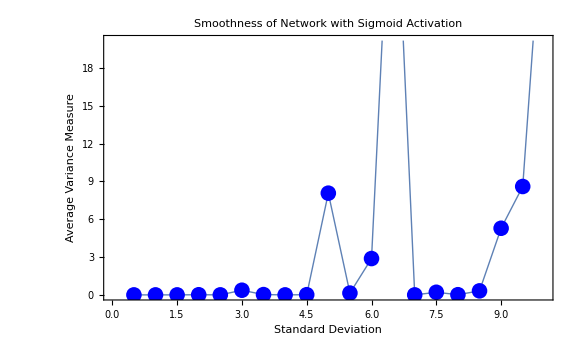

{0.5,7.5}

```mathematica
normalPlotVariance[LogisticSigmoid,3,Blue,"Smoothness of Network with Sigmoid Activation for Depth 3"]
```

## Gamma Distributions

### Defining Gamma Distribution Function

```mathematica
gammaNetworkPlot[activations_,depths_, alpha_, beta_]:=Module[{netPlots,netInit,f,plots,act,depth},netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[4];
SeedRandom[1234];
plots=Append[Prepend[netPlots,""]]@Table[Prepend[Text[act/. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->GammaDistribution[alpha,beta],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths}],{act,activations}];
Grid[plots]
]
```

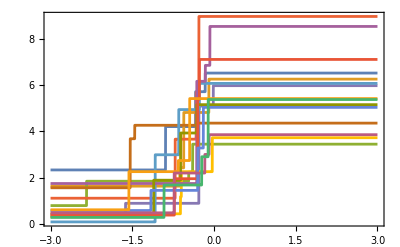
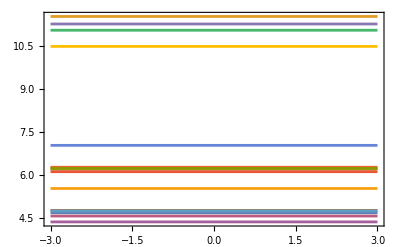
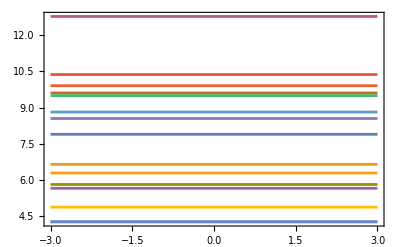
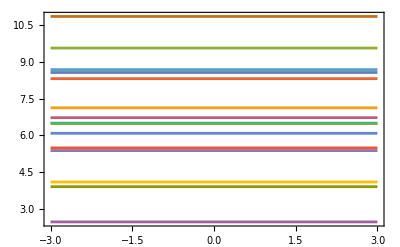
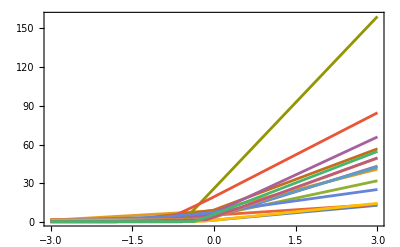
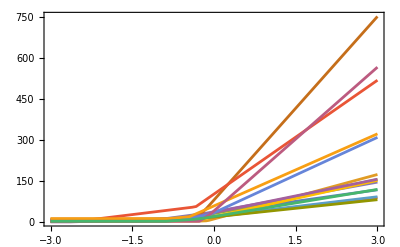
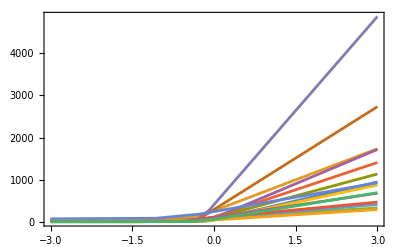
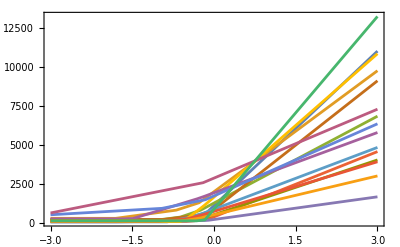
Threshold | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Ramp | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Tanh | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Sin | -Graphics- | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
gammaNetworkPlot[{Function[x,If[x>0,1,0]],Ramp,Tanh,Sin,LogisticSigmoid},{1,2,3,4}, 2, 1]
```

#### Explanation

As the graph above shows, the gamma distribution has the output maintaining the rough shape of the activation function, with a slight exception for the Sin function. Why is this?
Another question: Why doesn’t Ramp ever lose its gradients with this distribution but does with the normal distribution? Answer: Gamma distributions limit themselves to positive values, and this prevents the Ramp function from ever entering the saturated range where all values go to 0, and the gradient approaches zero. If Ramp is working with positive values only, then the gradient stays at 1, and this also prevents and exploding gradient that would create output graphs with obscene frequencies as can be observed with the Sin function. Now, why does Logistic Sigmoid begin to lose gradients so quickly? Well, while Ramp’s saturated range is for values close to zero, the graph of Logistic Sigmoid shows us that its first derivative approaches 0 for large positive values, which is what initializing weights from a gamma distribution results in. Because of this the gradients almost immediately approach zero, and the Logistic Sigmoid activation function flat-lines faster than it did for a normal distribution. Very similar logic applies for the Thresholding function, but there is another surprising result relating to this specific function in conjunction with the Tanh function. More specifically, why does the Tanh function begin to resemble a thresholding function at higher neural network depths? So, Tanh returns values close to 1 for large positive values and values close to -1 for large negative values. With a higher network depth, we’re applying Tanh again and again, and this pushes the outputs further and further toward one of these two regions, and the network begins to output almost exclusively either 1 or -1. Now why does Sin reach insanely high frequencies? So when we stack multiple layers of a Sin function in a neural network, each layer is processing a linear combination of the outputs of a sin function, and this results in compositions of Sin functions that can lead to harmonics (essentially frequency multipliers). This is what it looks like mathematically:
 


where  represents the matrix of weights at layer  in the neural network and  represents the bias vector at layer .

### Finding Optimal Alpha and Beta to prevent Gradient Loss

```mathematica
gammaInitializeNet[alpha_,beta_,activation_,depth_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->GammaDistribution[alpha,beta],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
```

```mathematica
gammaEvaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
```

```mathematica
alphas=Range[0.5,5,0.5];
betas=Range[0.5,5,0.5];
gammaMeasureVariance[activation_,depth_]:=Flatten[Table[With[{netInit=gammaInitializeNet[alpha,beta,activation,depth]},{{alpha,beta},Mean[Table[Module[{outputs=gammaEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]}],{alpha,alphas},{beta,betas}],1];
gammaMeasureVarianceplotted[activation_,depth_]:=Table[With[{netInit=gammaInitializeNet[alpha,beta,activation,depth]},{alpha,beta,Mean[Table[Module[{outputs=gammaEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]}],{alpha,alphas},{beta,betas}];
```

```mathematica
gammaOptimalParams[activation_,depth_]:=Module[{varianceMeasures,minParams,maxParams},varianceMeasures=gammaMeasureVariance[activation,depth];
minParams=varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],1]]]];
maxParams=varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],-1]]]];
{minParams[[1]],maxParams[[1]]}];
```

```mathematica
gammaPlotVariance[activation_,depth_]:=Module[{varianceMeasures,alphaBetaVariance},varianceMeasures=gammaMeasureVarianceplotted[activation,depth];
alphaBetaVariance=Partition[varianceMeasures[[All,3]],Length[betas]];
ListPlot3D[alphaBetaVariance,DataRange->{{First[alphas],Last[alphas]},{First[betas],Last[betas]}},PlotLabel->"Variance Measure for Gamma Distribution",PlotStyle->"Surface",ColorFunction->"Rainbow",InterpolationOrder->2,Mesh->True,ImageSize->Large]];
```

```mathematica
depth=3;
activation=LogisticSigmoid;
gammaOptimalParams[activation,depth]
```

```mathematica
gammaPlotVariance[activation,depth]
```

-Graphics3D-

## Uniform Distributions

### Defining a Function for Uniform Distribution

```mathematica
ClearAll[ThresholdNetworkPlotUniform]
ThresholdNetworkPlotUniform[activations_,depths_,range_]:=Module[{netPlots,netInit,f,plots,act,depth},netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[8];
SeedRandom[1234];
plots=Append[Prepend[netPlots,""]]@Table[Prepend[Text[act/. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->UniformDistribution[{-range,range}],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths}],{act,activations}];
Grid[plots]
]
```

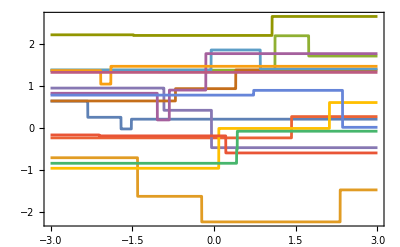
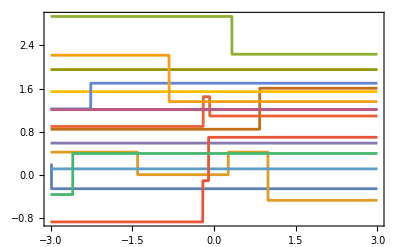
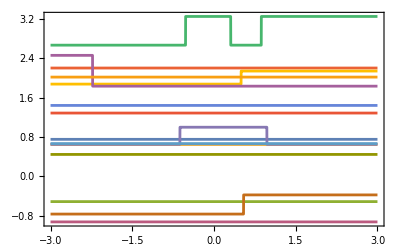
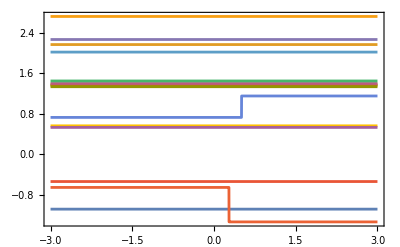
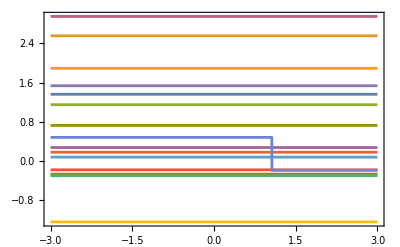
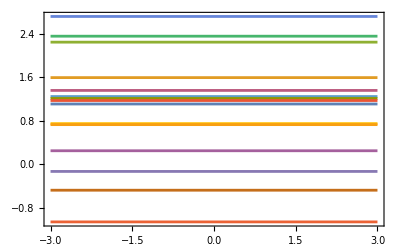
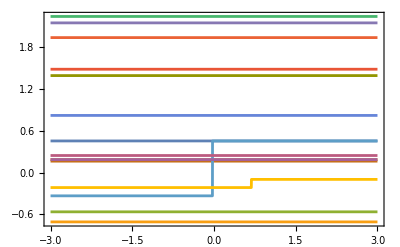
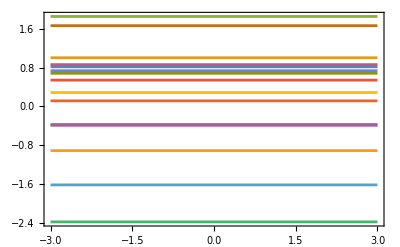
Threshold | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Ramp | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Tanh | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Sin | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

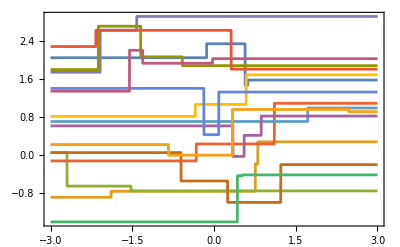
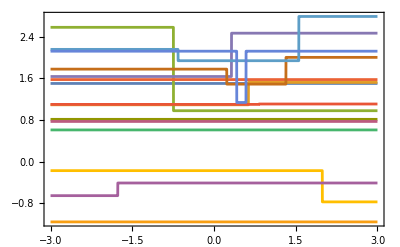
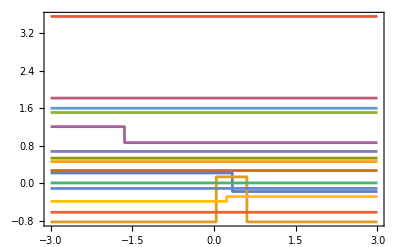
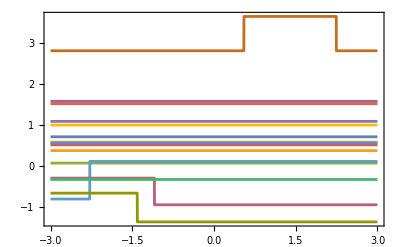
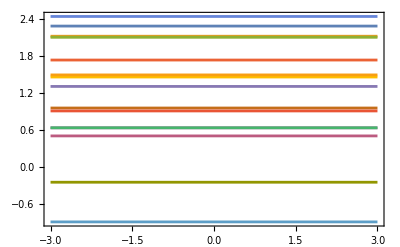
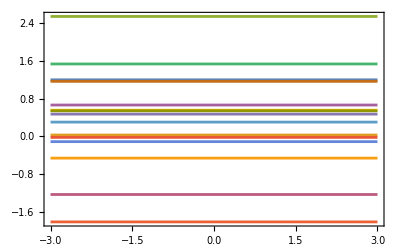
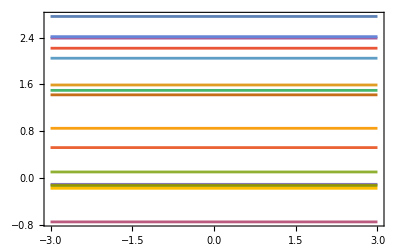
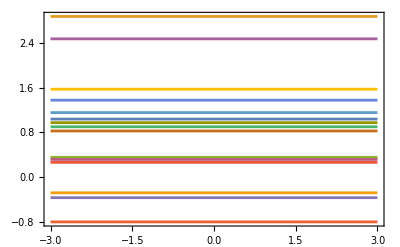
Threshold | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Ramp | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Tanh | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Sin | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
ThresholdNetworkPlotUniform[{Function[x,If[x>0,1,0]],Ramp,Tanh,Sin,LogisticSigmoid},{1,2,3,4,5,6,7,8},1]
```

### Explanation

Obviously, since we are generating the weights from a uniform distribution, any given weight is equally likely to be any number between  and , in this case , -1 and 1. The most striking thing about this collection of output graphs is their flatness. While most of the graphs don’t actually flat-line, their outputs have a much lower frequency than the counterparts that are created by weights initialized from normal or gamma distributions. Why does this happen? Some of the activation functions that we are testing here are non-linear and sensitive to small changes in input (namely Sin). Because the uniform distribution has a lower variance than the normal or gamma distribution, the weights we are initializing will likely have a lower variance than usual, and non-linear functions like Sin or Tanh will be less likely to reach extreme values. Now, the question of whether or not this is a good thing is more complicated. Having these less extreme output graphs lessens the danger of exploding gradients and can stabilize the training process and can be useful in layers that are intended to provide a more predictable output, but on the other hand, having the output graphs be too flat can mean that the neural network won’t be able to fit as well to complex data. At high enough depths (nearer to 10) almost all the activation functions experience gradient loss, so initializing with a uniform distribution doesn’t seem compatible with complex neural network structures.